NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

-Graphics3D-

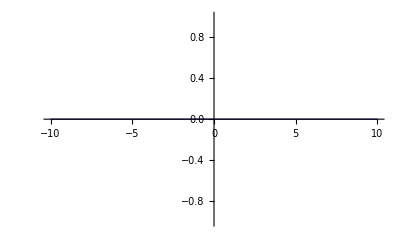

```mathematica
ClearAll["Global`*"]
ℏ =1;
m=1;
λ =1;
s=10;
k =1;
v=0.0;
d=10;
ω =ℏ;
A= 1;
time = 100;
V[x]=v*(Tanh[s(x+k)]-Tanh[s(x-k)]);

Eq=-((ℏ)^2/2m)D[u[x,t],{x,2}]+V[x]*u[x,t]-I*D[u[x,t],{t,1}]==0;

Bq={ u[-d,t]==A,Derivative[1,0][u][10d,t]==0,u[x,0]==0};
 
Sol=NDSolve[{Eq,Bq},u[x,t],{t,0,time},{x,-d,10d},MaxSteps->500000,MaxSteps->10^-2,Method->"Adams"][[1,1]];

Manipulate[Plot[Abs[Evaluate[u[x,t]/.Sol /.t ->j]]^2,{x,-d,d},PlotRange->All,PlotPoints->25,MaxRecursion->5],{j,0,time}]

Plot3D[Abs[Evaluate[u[x,t]/.Sol ]]^2,{x,-d,d},{t,0,time},PlotRange->All,PlotPoints->25,MaxRecursion->5]

Plot[Evaluate[V[x]],{x,-d,d},PlotRange->All,PlotPoints->25,MaxRecursion->5]
```